# Visualização de Dados com Mathematica

## Código Fonte do Livro

WTT 2010 - Universidade Presbiteriana Mackenzie

Mini curso: 27/05/2010 - 14hs - 3 horas duração - Lab 14 - sala 8 

Prof. Daniel S. Carvalho - Advisor Tecnologia
daniel.carvalho@advisor.com.br
danielscarvalho@gmail.com

Prof. Dr. Pedro P. B. Oliveira - Mackenzie
pedrob@mackenzie.br

Mini curso ministrado em laboratório com o software Mathematica 7 e acesso a Internet. 
Cada aluno em um equipamento.
Os alunos acompanham e desenvolvem o material ao longo do curso conforme segue.
Material atualizado para a versão mais recente Mathematica 9.0 em 2013.
Há funções apresentadas nesse NB que não são abordados no capítulo do livro.

## Introdução

## Princípios e funções básicas

```mathematica
Plus[1,2]
```

3

```mathematica
1+2
```

```mathematica
(1+3*5)/-10
```

-8/5

```mathematica
Table[x,{10}]
```

{2,2,2,2,2,2,2,2,2,2}

```mathematica
Table[x,{x,1,10,1}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Table[1/x,{x,1,10,1}]
```

{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10}

```mathematica
FullForm[i+j+ k]
```

Plus[i,j,k]

```mathematica
?Table
```

RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]], "}"}]}], "]"}] generates a list of SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]] copies of StyleBox["expr", "TI"]. 
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a list of the values of StyleBox["expr", "TI"] when StyleBox["i", "TI"] runs from 1 to SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] starts with RowBox[{StyleBox["i", "TI"], "=", SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]]}]. 
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]], ",", StyleBox["di", "TI"]}], "}"}]}], "]"}] uses steps StyleBox["di", "TI"]. 
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "}"}]}], "]"}] uses the successive values SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], SubscriptBox[StyleBox["i", "TI"], StyleBox["2", "TR"]], ….
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["j", "TI"], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] gives a nested list. The list associated with StyleBox["i", "TI"] is outermost.

```mathematica
?Ta*
```

```mathematica
10/3
```

10/3

```mathematica
N[10/3]
```

3.33333

```mathematica
N[10/3,100]
```

3.333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333

```mathematica
Pi
```

π

```mathematica
N[Pi,10]
```

3.141592654

```mathematica
N[Pi,100]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

```mathematica
Prime[30]
```

113

```mathematica
Fibonacci[100]
```

354224848179261915075

```mathematica
Abs[-10]
```

10

```mathematica
Mod[3,2]
```

1

```mathematica
Sin[Pi]
```

0

```mathematica
Cos[2 Pi]
```

1

```mathematica
Sqrt[2]
```

√2

```mathematica
Sqrt[4]
```

2

```mathematica
TraditionalForm[  2/
(x Pi /( -(3 I) 
^(Sqrt[x + E])) )]
```

-(2 (3 ⅈ)^(√(x+ⅇ)))/(π x)

```mathematica
RealDigits[11/9,10,10]
```

{{1,2,2,2,2,2,2,2,2,2},1}

```mathematica
RandomInteger[10]
```

4

```mathematica
RandomInteger[110]
```

64

```mathematica
IntegerPart[Pi]
```

3

```mathematica
IntegerPart[E]
```

2

```mathematica
IntegerPart[14.89]
```

14

```mathematica
IntegerDigits[1974]
```

{1,9,7,4}

```mathematica
x=2;
If[x==1,A,B]
```

B

```mathematica
RealDigits[3.1415]
```

{{3,1,4,1,5,0,0,0,0,0,0,0,0,0,0,0},1}

## Manipulação de listas

```mathematica
Rule[a,1]
```

a→1

```mathematica
a-> 1
```

a→1

```mathematica
ReplaceAll[{a,b},{a-> 1, b-> 2}]
```

{1,2}

```mathematica
Flatten[{{i,j,k},{x,y,z}}]
```

{i,j,k,x,y,z}

```mathematica
Map[f,{x,y,z}]
```

{f[x],f[y],f[z]}

```mathematica
f/@{a, b ,c}
```

{f[a],f[b],f[c]}

```mathematica
Partition[{1,2,a,b,Π,α,β},2]
```

{{1,2},{a,b},{Π,α}}

```mathematica
Dimensions[{{1,2,3,4},
{a,b,c,d}}]
```

{2,4}

```mathematica
Apply[f,{a,b,c,d}]
```

f[a,b,c,d]

```mathematica
f@@{x, y,z}
```

f[x,y,z]

```mathematica
f@@@ {i,{ j, k}}
```

{i,f[j,k]}

```mathematica
Drop[{a , b ,c, d},-1]
```

{a,b,c}

```mathematica
Drop[{a , b ,c, d},2]
```

{c,d}

```mathematica
Riffle[{1,2,3},f]
```

{1,f,2,f,3}

```mathematica
Riffle[{1,2,3,4},{a ,b,c,d}]
```

{1,a,2,b,3,c,4,d}

```mathematica
Prepend[{i,j,k},Z]
```

{Z,i,j,k}

```mathematica
Append[{i,j,k},Z]
```

{i,j,k,Z}

```mathematica
p
```

```mathematica
lst={A,B,C,D};
Part[lst,1]
```

A

```mathematica
lst[[1]]
```

A

```mathematica
lst⟦3⟧
```

C

```mathematica
lst⟦2;;3⟧
```

{B,C}

```mathematica
resultado = Sqrt[3]/2;
```

```mathematica
resultado
```

(√3)/2

## Declaração de funções

```mathematica
MyFunc[a_]:=Abs[ Sqrt[a]/Cos[a]];
```

```mathematica
MyFunc[8]
```

-2 √2 Sec[8]

```mathematica
TraditionalForm[MyFunc[x]]
```

Abs[√x sec(x)]

```mathematica
Table[MyFunc[x],{x,0,10,1}]
```

{0,Sec[1],-√2 Sec[2],-√3 Sec[3],-2 Sec[4],√5 Sec[5],√6 Sec[6],√7 Sec[7],-2 √2 Sec[8],-3 Sec[9],-√10 Sec[10]}

```mathematica
r=Table[MyFunc[x*y],{x,-1,1,.1},{y,-1,1,.1}];
```

```mathematica
Dimensions[r]
```

{21,21}

## Ferramentas de visualização

```mathematica
GraphicsGrid[{{
ArrayPlot[r,Frame-> None,Mesh-> True, PlotLabel-> Text[Style["ArrayPlot",FontFamily -> "Courier"]]],
ListPlot3D[r,PlotLabel-> Text[Style["ListPlot3D",FontFamily -> "Courier"]]] },{
ListDensityPlot[r,PlotLabel-> Text[Style["ListDensityPlot",FontFamily -> "Courier"]]],
ListContourPlot[r,PlotLabel-> Text[Style["ListContourPlot",FontFamily -> "Courier"]]]}},Frame-> All]
```

-Graphics-

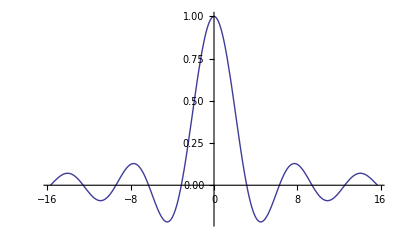

```mathematica
Plot[Sinc[x],
{x,5 Pi,-5 Pi},
PlotStyle-> Thick,PlotRange-> All]
```

```mathematica
ListPlot3D[Table[Sinc[x]*Sinc[y],
{x,-10,10,.1},
{y,-10,10,.1}],
PlotRange-> All]
```

-Graphics3D-

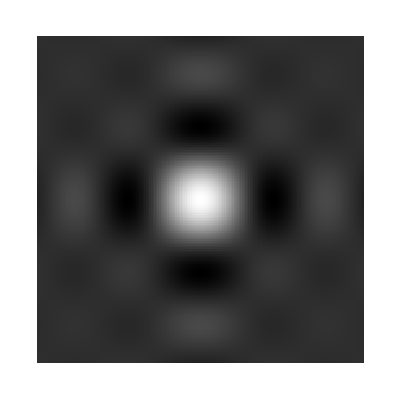

```mathematica
ArrayPlot[Table[Sinc[x]*Sinc[y],
{x,-10,10,.1},
{y,-10,10,.1}],ColorFunction->GrayLevel]
```

```mathematica
Manipulate[
ArrayPlot[Table[Sinc[x]*Sinc[y],
{x,-10,10,.1},
{y,-10,10,.1}],
 ColorFunction-> color],
{color,ColorData["Gradients"]}]
```

```mathematica
Manipulate[
ArrayPlot[Table[Sinc[x]*Sinc[y],
{x,-10,10,.1},
{y,-10,10,.1}],
 ColorFunction-> color],
{color,ColorData["Gradients"],ControlType-> Slider}]
```

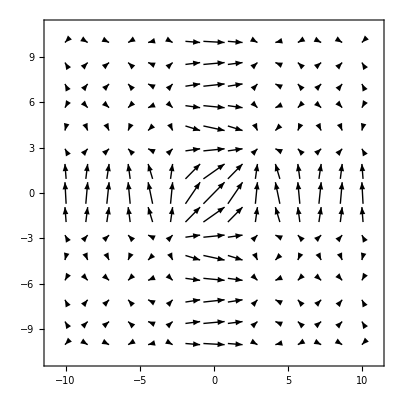

```mathematica
VectorPlot[{Sinc[x],Sinc[y]},
{x,-10,10},
{y,-10,10},
VectorStyle-> Black]
```

```mathematica
scTable=Table[{Sin[x],Cos[y]},
{x,-10,10,.1},
{y,-10,10,.1}];
```

```mathematica
Dimensions[scTable]
```

{201,201,2}

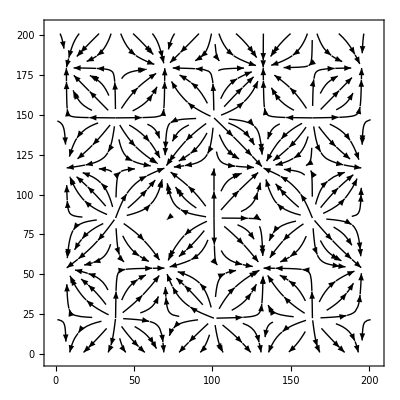

```mathematica
ListStreamPlot[scTable,StreamStyle-> Black]
```

```mathematica
Show[ArrayPlot[scTable,ColorFunction-> GrayLevel],
ListStreamPlot[scTable]]
```

ArrayPlot::mat: Argument scTable at position 1 is not a list of lists.

Visualization`Core`ListStreamPlot::vfldata: scTable is not a valid vector field dataset or a valid list of datasets.

Show::gcomb: Could not combine the graphics objects in Show[ArrayPlot[scTable, ColorFunction → GrayLevel], ListStreamPlot[scTable]].

Show[ArrayPlot[scTable,ColorFunction→GrayLevel],ListStreamPlot[scTable]]

```mathematica
Plot3D[Sin[x]*Cos[y],
{x,-10,10},
{y,-10,10}]
```

-Graphics3D-

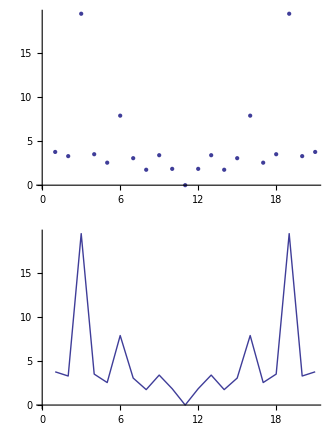

```mathematica
GraphicsGrid[{{ListPlot[#]},
{ListLinePlot[#]}},
Frame-> All]&[Table[MyFunc[x],{x,-10,10}]]
```

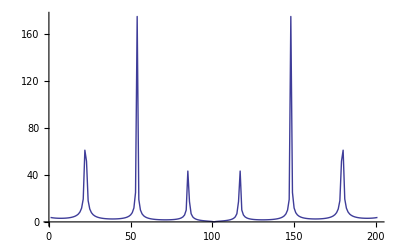

```mathematica
ListLinePlot[
Table[MyFunc[x],
{x,-10,10, .1}],PlotRange -> All]
```

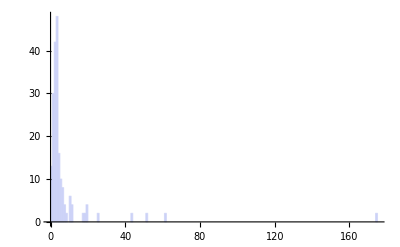

```mathematica
Histogram[
Table[MyFunc[x],
{x,-10,10,.1}],{1},PlotRange-> All]
```

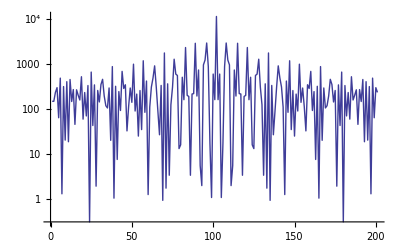

```mathematica
ListLogPlot[RotateLeft[Abs[Fourier[Table[MyFunc[x],{x,-10,10,.1}]]]^2,100],PlotRange-> All,Joined->True] (* Power Spectrum *)
```

## Grafos

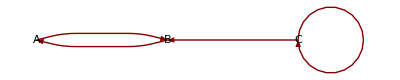

```mathematica
GraphPlot[{A-> B,C-> B,B-> A, C->C },DirectedEdges->True,
VertexLabeling->True]
```

#### Função RuleIt

```mathematica
RuleIt[dataList_]:=Rule@@@Partition[Riffle[Drop[#,-1],Drop[#,1]],2]& [dataList];
```

```mathematica
RuleIt[{I,J,K,L}]
```

{ⅈ→J,J→K,K→L}

```mathematica
z=RuleIt[Table[RandomInteger[x],{x,10}]]
```

{1→0,0→0,0→1,1→2,2→5,5→1,1→4,4→4,4→8}

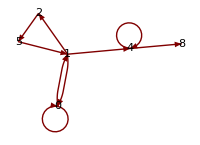

```mathematica
GraphPlot[z,
ImageSize-> 200,
DirectedEdges->True,
VertexLabeling->True]
```

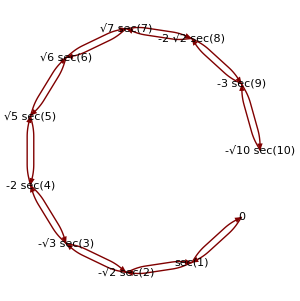

```mathematica
GraphPlot[RuleIt[Table[MyFunc[x],{x,-10,10,1}]],
ImageSize-> 300,
DirectedEdges->True,
VertexLabeling->True,
Method->"CircularEmbedding"]
```

```mathematica
(* GetDigits[real_, digits_]:=IntegerDigits[IntegerPart[N[real,digits]*10^digits]]; *)
```

```mathematica
GetDigits[real_, digits_]:=
If[RealDigits[real,10,digits-1]⟦2⟧==0,
Prepend[Drop[RealDigits[real,10,digits]⟦1⟧,-1],0],
RealDigits[real,10,digits]⟦1⟧]
```

```mathematica
GetDigits[0.2345,10]
```

{0,2,3,4,5,0,0,0,0,0}

```mathematica
GetDigits[1/7,10]
```

{0,1,4,2,8,5,7,1,4,2}

```mathematica
GetDigits[Pi,10]
```

{3,1,4,1,5,9,2,6,5,3}

```mathematica
GetDigits[137/999,30]
```

{0,1,3,7,1,3,7,1,3,7,1,3,7,1,3,7,1,3,7,1,3,7,1,3,7,1,3,7,1,3}

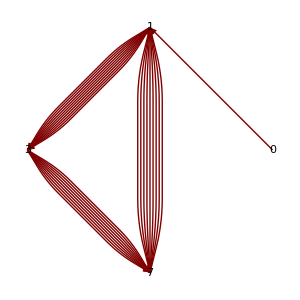

```mathematica
GraphPlot[RuleIt[GetDigits[137/999,30]],
ImageSize-> 300,
DirectedEdges->True,
Method->"CircularEmbedding",
VertexLabeling->True]
```

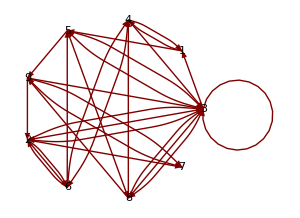

```mathematica
GraphPlot[RuleIt[GetDigits[Pi,30]],
ImageSize-> 300,
DirectedEdges->True,
Method->"CircularEmbedding",
VertexLabeling->True]
```

```mathematica
Total[GetDigits[E,100]]==
Total[RealDigits[N[E,100]][[1]]]
```

True

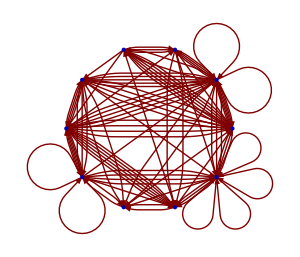

```mathematica
GraphPlot[RuleIt[GetDigits[E,100]],
ImageSize-> 300,
DirectedEdges->True,
Method->"CircularEmbedding"]
```

## Funções matemáticas simples com comportamento complexo (sofisticado)

```mathematica
Clear[x]
```

```mathematica
Func2[x_,y_, power_] := Abs[Mod[(x+y I)^-power,2]];
```

Power::infy: Infinite expression 1/(0.  + 0.\ ⅈ)^3 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity - ComplexInfinity encountered.

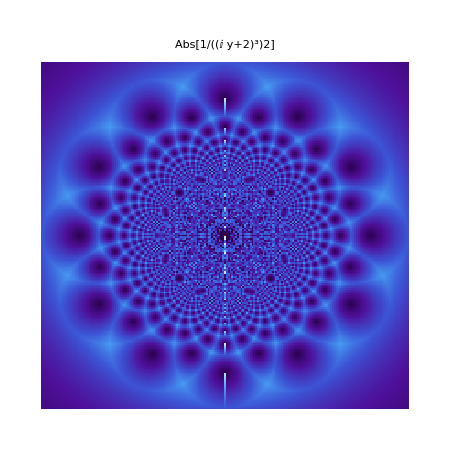

```mathematica
ArrayPlot[Table[
Func2[x,y,3]
,{x,-1,1,0.01},{y,-1,1,0.01}],
Mesh->False,Frame->False,ColorFunction-> "DeepSeaColors",PlotLabel->TraditionalForm[Func2[x,y,3]]]
```

## Alinhamento de sequência de DNA

```mathematica
s1=GenomeData["H2AFB1","FullSequence"]
```

CGCCCAGCATGCCGAGGAGGAGGAGACGCCGAGGGTCCTCCGGTGCTGGCGGCCGGGGGCGGACCTGCTCTCGCACCGTCCGAGCGGAGCTTTCGTTTTCAGTGAGCCAGGTGGAGCGCAGTCTACGGGAGGGCCACTACGCTCAGCGCCTGAGTCGCACGGCGCCGGTCTACCTCGCTGCGGTTATTGAGTACCTGACGGCCAAGGTCCCGGAGCTGGCGGGCAACGAGGCCCAGAACAGCGGAGAGCGGAACATCACTCCCCTGCTGCTGGACATGGTGGTTCACAACGACAGGCTACTGAGCACCCTTTTCAACACGACCACCATCTCTCAAGTGGCCCCTGGCGAGGACTAGCTTCTGACACCCGGCCCCTGGGACCTGACAGGTCCACTCGTCCACCCACCCGGCCCCAAATCCCCCGGCCTGAACCCCCGGCCTTAAACACCCTCCCCCCACAACCCAGGCCCCAAAGTCTTGGGCCTTCATTAATTCTGTCAATAAAATGTTTCAAGGAA

```mathematica
s3=GenomeData["H2AFB3","FullSequence"]
```

CGCCCAGCATGCCGAGGAGGAGGAGACGCCGAGGGTCCTCCGGTGCTGGCGGCCGGGGGCGGACCTGCTCTCGCACCGTCCGAGCGGAGCTTTCGTTTTCAGTGAGCCAGGTGGAGCGCAGTCTACGGGAGGGCCACTACGCTCAGCGCCTGAGTCGCACGGCGCCGGTCTACCTCGCTGCGGTTATTGAGTACCTGACGGCCAAGGTCCTGGAGCTGGCGGGCAACGAGGCCCAGAACAGCGGAGAGCGGAACATCACTCCCCTGCTGCTGGACATGGTGGTTCACAACGACAGGCTACTGAGCACCCTTTTCAACACGACCACCATCTCTCAAGTGGCCCCTGGCGAGGACTAGCTTCTGACACCCGGCCCCTGGGACCTGACAGGTCCACTCGTCCACCCACCCGGCCCCAAATCCCCCGGCCTGAACCCCCGGCCTTAAACACCCTCCCCCCACAACCCAGGCCCCAAAGTCTTGGGCCTTCATTAATTCTGTCAATAAAATGTTTCAAGGAA

```mathematica
StringLength[s1]
```

517

```mathematica
StringLength[s3]
```

517

```mathematica
s1c=Characters[s1][[200;;299]]
```

{G,G,C,C,A,A,G,G,T,C,C,C,G,G,A,G,C,T,G,G,C,G,G,G,C,A,A,C,G,A,G,G,C,C,C,A,G,A,A,C,A,G,C,G,G,A,G,A,G,C,G,G,A,A,C,A,T,C,A,C,T,C,C,C,C,T,G,C,T,G,C,T,G,G,A,C,A,T,G,G,T,G,G,T,T,C,A,C,A,A,C,G,A,C,A,G,G,C,T,A}

```mathematica
s3c=Characters[s3][[200;;299]]
```

{G,G,C,C,A,A,G,G,T,C,C,T,G,G,A,G,C,T,G,G,C,G,G,G,C,A,A,C,G,A,G,G,C,C,C,A,G,A,A,C,A,G,C,G,G,A,G,A,G,C,G,G,A,A,C,A,T,C,A,C,T,C,C,C,C,T,G,C,T,G,C,T,G,G,A,C,A,T,G,G,T,G,G,T,T,C,A,C,A,A,C,G,A,C,A,G,G,C,T,A}

```mathematica
s1c==s3c
```

False

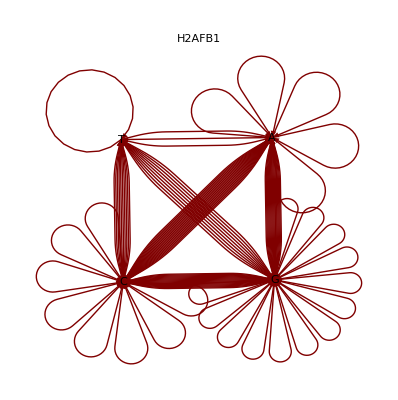

```mathematica
GraphPlot[RuleIt[s1c],VertexLabeling->True,DirectedEdges->True,PlotLabel->"H2AFB1"]
```

```mathematica
s1n=ReplaceAll[s1c,{"A"->1,"T"->2,"G"->3,"C"->4}]
```

{3,3,4,4,1,1,3,3,2,4,4,4,3,3,1,3,4,2,3,3,4,3,3,3,4,1,1,4,3,1,3,3,4,4,4,1,3,1,1,4,1,3,4,3,3,1,3,1,3,4,3,3,1,1,4,1,2,4,1,4,2,4,4,4,4,2,3,4,2,3,4,2,3,3,1,4,1,2,3,3,2,3,3,2,2,4,1,4,1,1,4,3,1,4,1,3,3,4,2,1}

```mathematica
s3n=ReplaceAll[s3c,{"A"->1,"T"->2,"G"->3,"C"->4}]
```

{3,3,4,4,1,1,3,3,2,4,4,2,3,3,1,3,4,2,3,3,4,3,3,3,4,1,1,4,3,1,3,3,4,4,4,1,3,1,1,4,1,3,4,3,3,1,3,1,3,4,3,3,1,1,4,1,2,4,1,4,2,4,4,4,4,2,3,4,2,3,4,2,3,3,1,4,1,2,3,3,2,3,3,2,2,4,1,4,1,1,4,3,1,4,1,3,3,4,2,1}

```mathematica
ArrayPlot[Table[UnitStep[-Norm[s1n[[x]]-s3n[[y]]]],{x,1,Length[s1n],1},{y,1,Length[s3n],1}],PixelConstrained->4, Frame-> None]
```

-Graphics-

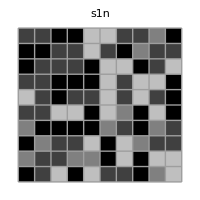
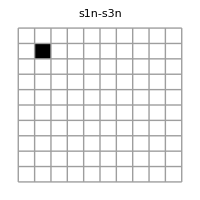
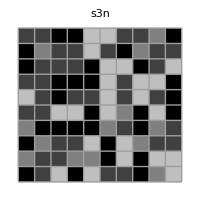
-Graphics- | -Graphics-
-Graphics- |

```mathematica
Grid[{{ArrayPlot[Partition[s1n,10],Frame->None,Mesh->True,ImageSize->200,PlotLabel->"s1n"],ArrayPlot[Partition[s1n-s3n,10],Frame->None,Mesh->True,ImageSize->200,PlotLabel->"s1n-s3n"]},{ArrayPlot[Partition[s3n,10],Frame->None,Mesh->True,ImageSize->200,PlotLabel->"s3n"],SpanFromAbove}},Frame->All,Alignment-> {Center,Center}]
```

```mathematica
SequenceAlignment[s1c,s3c]
```

{{G,G,C,C,A,A,G,G,T,C,C},{{C},{T}},{G,G,A,G,C,T,G,G,C,G,G,G,C,A,A,C,G,A,G,G,C,C,C,A,G,A,A,C,A,G,C,G,G,A,G,A,G,C,G,G,A,A,C,A,T,C,A,C,T,C,C,C,C,T,G,C,T,G,C,T,G,G,A,C,A,T,G,G,T,G,G,T,T,C,A,C,A,A,C,G,A,C,A,G,G,C,T,A}}

## Informações geográficas

```mathematica
CountryData["Brazil","GDP"]
```

1.3142×10^12

```mathematica
CountryData["Brazil","Population"]
```

1.91791×10^8

```mathematica
CountryData["Brazil","Area"]
```

8.51197×10^6

```mathematica
CountryData["SouthAmerica"]
```

{Argentina,Bolivia,Brazil,Chile,Colombia,Ecuador,FalklandIslands,FrenchGuiana,Guyana,Paraguay,Peru,Suriname,Uruguay,Venezuela}

```mathematica
CountryData["Brazil","Flag"]
```

-Graphics-

```mathematica
CountryData["Brazil",{"Population",{1999,2010}}]
```

{{{1999,1,1,0,0,0},1.71622×10^8},{{2000,1,1,0,0,0},1.74161×10^8},{{2001,1,1,0,0,0},1.76702×10^8},{{2002,1,1,0,0,0},1.79246×10^8},{{2003,1,1,0,0,0},1.81787×10^8},{{2004,1,1,0,0,0},1.84318×10^8},{{2005,1,1,0,0,0},1.86831×10^8},{{2006,1,1,0,0,0},1.89323×10^8},{{2007,1,1,0,0,0},1.91791×10^8}}

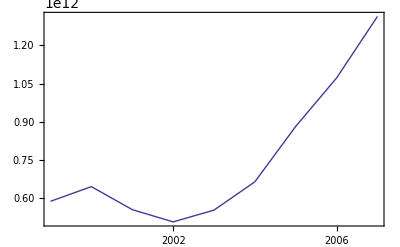

```mathematica
DateListPlot[CountryData["Brazil",{"GDP",{1999,2010}}],Joined->True]
```

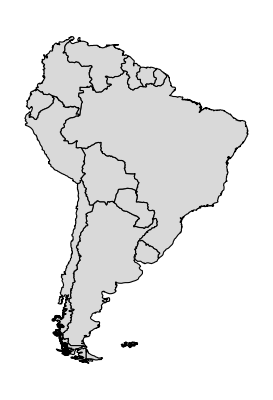

```mathematica
Graphics[{EdgeForm[Black],
LightGray,
CountryData[#,"Polygon"]&/@CountryData["SouthAmerica"]}]
```

```mathematica
CountryData["G8"]
TableForm[%]
```

{Canada,France,Germany,Italy,Japan,Russia,UnitedKingdom,UnitedStates}

Canada
France
Germany
Italy
Japan
Russia
UnitedKingdom
UnitedStates

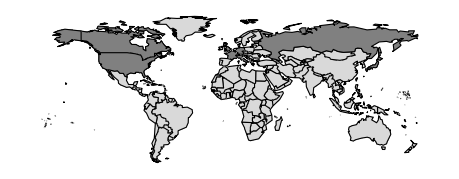

```mathematica
Graphics[{EdgeForm[Black],(* define a cor da borda/fronteiras *)
If[CountryData[#,"G8"],Gray,LightGray], (* define cor do mapa conforme a informação especificada*)
CountryData[#,"SchematicPolygon"]}&/@CountryData[]]
```

```mathematica
{CountryData[#,"Name"],CountryData[#,"GDP"]}&/@CountryData["SouthAmerica"]
Grid[%,Frame-> All, Alignment-> Left]
```

{{Argentina,2.62327×10^11},{Bolivia,1.31201×10^10},{Brazil,1.3142×10^12},{Chile,1.63915×10^11},{Colombia,1.68394×10^11},{Ecuador,4.44×10^10},{Falkland Islands,7.5×10^7},{French Guiana,1.551×10^9},{Guyana,1.05869×10^9},{Paraguay,1.20042×10^10},{Peru,1.08259×10^11},{Suriname,2.04409×10^9},{Uruguay,2.30867×10^10},{Venezuela,2.3672×10^11}}

Argentina | 2.62327×10^11
Bolivia | 1.31201×10^10
Brazil | 1.3142×10^12
Chile | 1.63915×10^11
Colombia | 1.68394×10^11
Ecuador | 4.44×10^10
Falkland Islands | 7.5×10^7
French Guiana | 1.551×10^9
Guyana | 1.05869×10^9
Paraguay | 1.20042×10^10
Peru | 1.08259×10^11
Suriname | 2.04409×10^9
Uruguay | 2.30867×10^10
Venezuela | 2.3672×10^11

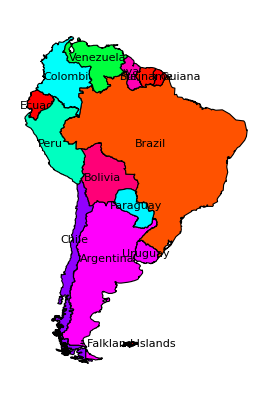

```mathematica
Graphics[{EdgeForm[Black],
Hue[CountryData[#,"GDP"]],
CountryData[#,"Polygon"],
Black,
Text[Style[CountryData[#,"Name"],FontFamily->"Arial"],Reverse[CountryData[#,"CenterCoordinates"]]]}&/@CountryData["SouthAmerica"]]
```

```mathematica
Length[CountryData[All]]
```

238

```mathematica
If[CountryData[#,"PortugueseSpeaking"],#]&/@CountryData[All]
Length[%]
```

{Null,Null,Null,Null,Null,Angola,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Brazil,Null,Null,Null,Null,Null,Null,Null,Null,CapeVerde,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,EastTimor,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,GuineaBissau,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Mozambique,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Portugal,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,SaoTomePrincipe,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

238

```mathematica
Select[If[CountryData[#,"PortugueseSpeaking"],#]&/@CountryData[All],StringQ]
```

{Angola,Brazil,CapeVerde,EastTimor,GuineaBissau,Mozambique,Portugal,SaoTomePrincipe}

```mathematica
DeleteCases[If[CountryData[#,"PortugueseSpeaking"],#]&/@CountryData[All],Null]
```

{Angola,Brazil,CapeVerde,EastTimor,GuineaBissau,Mozambique,Portugal,SaoTomePrincipe}

```mathematica
Graphics[DeleteCases[#,Null]&[{
If[CountryData[#,"PortugueseSpeaking"],Red,White],
EdgeForm[Black],
CountryData[#,"Polygon"],
Green,Thick,

If[CountryData[#,"PortugueseSpeaking"],
Circle[Reverse[CountryData[#,"CenterCoordinates"]],5],{}]

}&/@CountryData[All]]]
```

-Graphics-

## Informações sobre cidades

```mathematica
SPCityes={CityData[#,"Name"],CityData[#,"Population"]}&/@CityData[{All,"SaoPaulo","Brazil"}];
Grid[SPCityes⟦1;;20⟧ ,Frame-> All,Alignment-> Left]
```

Sao Paulo | 10021295
Guarulhos | 1169577
Campinas | 1031554
Sao Bernardo do Campo | 743372
Osasco | 677856
Santo Andre | 662373
Sao Jose dos Campos | 613764
Sorocaba | 558862
Ribeirao Preto | 551267
Santos | 411403
Diadema | 390633
Maua | 386069
Sao Jose do Rio Preto | 374699
Carapicuiba | 361112
Piracicaba | 342209
Itaquaquecetuba | 336679
Bauru | 335024
Moji das Cruzes | 325746
Sao Vicente | 324457
Jundiai | 321589

```mathematica
SPCityPos={Reverse[CityData[#,"Coordinates"]],CityData[#,"Population"]} &/@CityData[{All,"SaoPaulo","Brazil"}];

DeleteCases[DeleteCases[DeleteCases[SPCityPos,_Missing,Infinity],{},Infinity],Length[#]≤ 1 &,Infinity],

Graphics[Circle[#[[1]],Log[#[[2]]]*0.01]&/@ %]
```

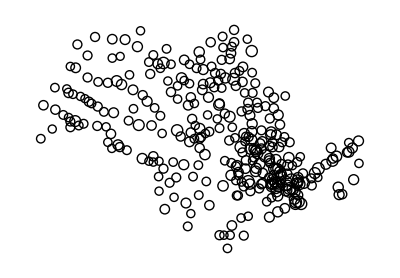

```mathematica
ListPlot3D[{
CityData[#,"Longitude"],
CityData[#,"Latitude"],
CityData[#,"Elevation"]}&/@CityData[{All,"SaoPaulo","Brazil"}],ColorFunction->Hue,MeshFunctions->{#3&}]
```

-Graphics3D-

## Informações sobre clima

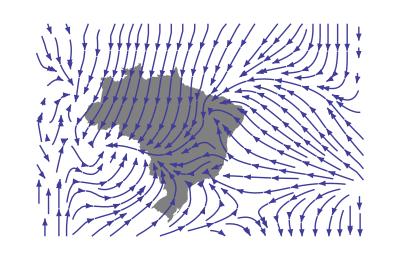

```mathematica
Show[Graphics[{
GrayLevel[.5],
CountryData["Brazil","Polygon"]}],
ListStreamPlot[
Table[{
Reverse[WeatherData[{y,x},"Coordinates"]],
-Through[{Sin,Cos}[WeatherData[{y,x},"WindDirection"] °]]},{x,-90 ,-10,5},
{y,-35, 8,5}]]]
```

```mathematica
wdata=Flatten[{#[[1,1;;2]],#[[2]]}]&/@WeatherData["Sao Paulo","MeanTemperature",{{1990},{2010},"Month"}];
```

```mathematica
ListPlot3D[wdata]
```

-Graphics3D-

## Obtendo dados precisos de fonte confiável

```mathematica
ExampleData[{"Geometry3D","SpaceShuttle"}]
```

-Graphics-

```mathematica
ExampleData[{"TestImage","Airplane"}]
```

-Graphics-

```mathematica
ExampleData[{"TestImage","Lena"}]
```

-Graphics-

## Processamento de Imagem

```mathematica
Blur[ExampleData[{"TestImage","Lena"}],10]
```

-Graphics-

```mathematica
EdgeDetect[ExampleData[{"TestImage","Lena"}],4]
```

-Graphics-

```mathematica
EdgeDetect[Import["https://www.google.com/images/srpr/logo11w.png"],10]
```

-Graphics-

```mathematica
ExampleData[{"TestImage","Tank"}]
ImageConvolve[%, 
{{-1,0,1},
{-2,0,2},
{-1,0,1}}]
```

-Graphics-

-Graphics-

```mathematica
ExampleData[{"TestImage","Mandrill"}]
ColorSeparate[%]
ArrayPlot[Log[Abs[Fourier[ImageData[#]]]],ColorFunction-> Hue]&/@%
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-}

## Bibliografia

Carvalho, Daniel de Souza. (2010) “Patterns from Math Rules Using Complex Numbers”, http://demonstrations.wolfram.com/PatternsFromMathRulesUsingComplexNumbers/.
	Friendly, Michael. (2009) “Milestones in the history of thematic cartography, statistical graphics, and data visualization”, http://www.math.yorku.ca/SCS/Gallery/milestone/.
	Fry, Ben. (2008) “Visualizing Data”, O' Reilly.
	Getz, Chonat.and Helmstedt, Janet.(2004) “Graphics with Mathematica : Fractals, Julia Sets, Patterns and Nutural Forms”, Elsevier.
	Mangano, Sal. (2010) “Mathematica Cookbook”.O' Reilly.
	Marwan, N., Romano, M.C., Thiel, M.and Kurths, J. (2007) “Recurrence Plots for the Analysis of Complex Systems”, Physics Reports, 438 (5 - 6), 237 - 329.
	Post, Frits H.Nielson, Gregory M.and Bonneau, Georges - Pierre. (2002) “Data Visualization : The State of The Art”, Proceedings of the 4 th Dagstuhl Seminar on Scientiﬁc Visualization.
	Segaran, Toby. and Hammerbacher, Jeff. (2009) “Beautiful Data - The Stories Behind Elegant Data Solutions”, O' Reilly.
	Trott, Michael. (2004) “The Mathematica GuideBook for Graphics”, Springer.
	Tufte, Edward R. (1991) “Envisioning Information”, Graphics Press.
	Wolfram, S. (2008) “Wolfram Mathematica Tutorial Collection : Visualization and Graphics”, Wolfram Media.
	Wolfram, S. (2010) “The Wolfram Demonstrations Project”, http://demonstrations.wolfram.com/. 
	Wolfram, S. (2010 b) “Wolfram Mathematica 7 Documentation Center”, http://reference.wolfram.com/mathematica/guide/Mathematica.html.
	Wright, Helen. (2007) “Introduction to Scientific Visualization”, Springer.